```mathematica
ode1={y''[x]*y[x]^2==y[x]^2+y[x]+1,y'[0]==0, y[0]==0}
```

{y[x]^2 y''[x]==1+y[x]+y[x]^2,y'[0]==0,y[0]==0}

```mathematica
sol=DSolve[ode1,{y[x]},{x,10,100}]
```

Power::infy: Infinite expression 1/0.^2 encountered.

NDSolve::ndnum: Encountered non-numerical value for a derivative at x == 0..

NDSolve[{y[x]^2 y''[x]==1+y[x]+y[x]^2,y'[0]==0,y[0]==0},{y[x]},{x,10,100}]

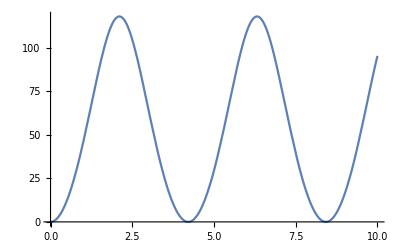

```mathematica
Plot[y[x]/.sol,{x,0,10}]
```

```mathematica
'
```